# 38: Conjugate Gradients (CG) Theorems

## Quadratic Form for b and Symmetric A

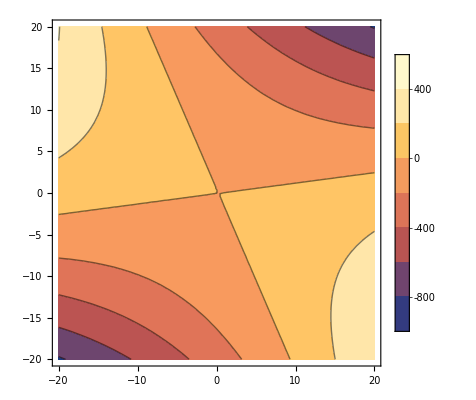

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
b=RandomReal[{-1,1},m];
f[x_]:= 0.5 x.A.x-b.x
ContourPlot[f[{x1,x2}],{x1,-20,20},{x2,-20,20},
PlotLegends->Automatic]
Plot3D[f[{x1,x2}],{x1,-20,20},{x2,-20,20},
PlotLegends->Automatic];
```

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
Eigenvalues[A]
b=RandomReal[{-1,1},m];
f[x_]:= 0.5 x.A.x-b.x
ContourPlot3D[f[{x1,x2,x3}],{x1,-20,20},{x2,-20,20},{x3,-20,20},
PlotLegends->Automatic,Contours->5]
```

{1.96362,0.602472,0.367383}

-Graphics3D-

## SPD A and Quadratic Forms

For an SPD matrix A minimizing the quadratic form
	f(x)=1/2 x.A.x-b.x+c
is the same as solving A.x=b.  To see this all you need to do is note that
	∇f=A.x-b
and that for z=A^-1 b we have 
	f(p)=f(z)+1/2(p-z).A.(p-z)

This means we can solve A.x=b by heading down hill in the function in f.

Note: 
1) We can compute the residual r(x)=A.x-b.  
2) The straight downhill direction is just the negative gradient -r(x).  
3) For any initially downhill direction p the function f(x+α p) stops going downhill and starts going uphill at some point α^*. 
4) Since 
	f(x + α p) = 1/2(x+α p).A.(x + α p)-b.(x+α p)+c=α^2/2 p.A.p+α (x.A.p-x.p) +1/2 x.A.x- b.x+c
  we have
  	d/dα f(x+α p)=α p.A.p + (x.A.p-x.p)
  and 
  	α^*=(x.A.p-x.p)/(p.A.p)
  5) Conjugate Gradients consists of always going as far downhill as you should i.e. as far as α^* and making sure you do not tack.  We are going to make sure that our directions are conjugate p_i.A.p_j=0 if i≠j

## A.x=b via Conjugate Gradients

For A ϵ ℝ^(m×m) is Symmetric and Positive Definite (SPD) ||x(||)_(CG(A)):=√(x.A.x) is a norm!   Conjugate Gradients iteratively minimizes the residual in this tailored norm.

### Algorithm 38.1

Conjugate gradients (Algorithm 38.1) is simply this exact line search minimization starting from the predetermined  initial guess x_0=OverVector[0].  Here is the pseudo code from the text

Conjugate Gradients
x_0=0, r_0=b, p_0=r_0
for n in 1, 2, 3, ...
	α_n=(r_(n-1).r_(n-1))/(p_(n-1).A.p_(n-1))
	x_n=x_(n-1)+α_n p_(n-1)
	r_n=r_(n-1)-α_n A.p_(n-1)
	β_n=(r_n.r_n)/(r_(n-1).r_(n-1))
	p_n=r_n+β_n p_(n-1)

Here is an implementation of a single step

```mathematica
CGStep[A_][{xIn_,rIn_,pIn_}]:=Module[{ApIn=A.pIn,α,β,xOut,rOut,pOut},
α=(rIn.rIn)/(pIn.ApIn);
xOut=xIn+α pIn;
rOut=rIn - α ApIn;
β = (rOut.rOut)/(rIn.rIn); 
pOut=rOut+β pIn;
{xOut,rOut,pOut}]

CGNorm[A_][x_]:= √(x.A.x)
```

Import an SPD matrix A from Matrix market, define a synthetic solution x_∞, and compute the matching RHS.

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"]
m=Length[A];
(* Create an identifiable synthetic solution and matching RHS *)
xInf=Table[Cos[0.1 i],{i,m}];b=A.xInf;
(* Initialize and run CG loop *)
MaxIter=82;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
(* Visualize the Convergence *)
TabView[{
"x_MaxIter"->ListPlot[{xrpData⟦-1,1⟧,xInf}],
"||x-x_∞(||)_(CG (A))"->ListLogPlot[Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧]],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

SparseArray[…]

1234

Slow but very steady is what I would say here. Remember, preconditioners are essential!

```mathematica
TabView[{
"Diagonal A"->ListLogPlot[Diagonal[A],PlotRange->All],
"A"->MatrixPlot[A,PlotLegends->Automatic]}]
```

12

## Optimality and Convergence

Just like the other Krylov algorithms we have looked at CG has an optimality property for polynomials.  Not surprisingly CG is optimal in the tailored norm. Theorem 38.3 shows that CG constructs the polynomial that minimizes ||p_n(A)(x_∞-x_0)(||)_(CG(A)) over the set of polynomials with p(0)=1 where our initial guess x_0 is always the zero vector. The trick to seeing this is to use the orthogonal eigen basis {v_1,v_2,…,v_m} for A and note that 
	||p(A)(x_∞-x_0)(||)_(CG(A))^2=∑_(j=1)^m a_j^2 λ_j * (p(λ_j))^2 and ||(x_∞-x_0)(||)_(CG(A))^2=∑_(j=1)^m a_j^2 λ_j
where x_∞-x_0=∑_(j=1)^m a_j v_j.  Just like before we get a useful expression for the appropriate scaled relative error
	(||x_∞-x_n(||)_(CG(A)))/(||x_∞-x_0(||)_(CG(A)))=minp∈𝒫_n (||p(A)(x_∞-x_0)(||)_(CG(A)))/(||x_∞-x_0(||)_(CG(A)))≤minp∈𝒫_n max_(λ∈Λ(A))|p(λ)|.

This has lots of useful consequences for matrices with clustered eigenvalues. The book presents two very different results.

The first theorem is a positive theorem which concerns  eigenvalues clustered as tightly as possible in the sense that there are only n "distinct" eigenvalues: the theorem says that CG converges in less than n-steps. The reason this is plausible is that a single CG step simultaneously resolves all directions in a scalar multiple of the identity. In practice, CG resolves tight clusters of eigenvalues almost simultaneously.  In practice, the theorem says that convergence is fast for matrices with a few “tight” eigenvalue clusters.

The second theorem is a worst case theorem which gives the slowest possible convergence rate for a spectrum with eigenvalues λ spread between 0<λ_min≤λ≤λ_max in terms of the condition number κ=λ_max/λ_min. The theorem is expressed as 
	 (||x_∞-x_n(||)_(CG(A)))/(||x_∞-x_0(||)_(CG(A)))≤2((√κ-1)/(√κ+1))^n∼(1-2/(√k))^n

### Clustered Examples

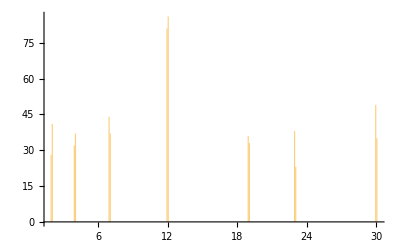

```mathematica
m=600;
ϵ=10^-4;
dist=MixtureDistribution[{1,1,1,2,1,1,1},
{NormalDistribution[2,ϵ],NormalDistribution[4,2ϵ],NormalDistribution[7,3ϵ],NormalDistribution[12,5ϵ],NormalDistribution[30,10ϵ],NormalDistribution[19,10ϵ],NormalDistribution[23,10ϵ]}];
λs=RandomVariate[dist,m];
Q=Orthogonalize[RandomReal[{-1,1},{m,m}]];
A=Q.DiagonalMatrix[λs].Qᵀ;
Histogram[λs,200]
```

```mathematica
xInf=RandomReal[{-1,1},m];
b=A.xInf;
MaxIter=50;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧],
"r"->MatrixPlot[xrpData⟦All,2⟧],
"p"-> MatrixPlot[xrpData⟦All,3⟧]
}]
TabView[{
"||x-x_∞(||)_(CG (A))"->ListLogPlot[Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧]],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

123

123

### Non-Clustered Examples

0.980198

700

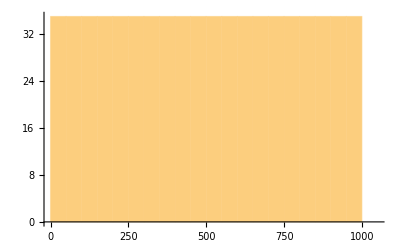

```mathematica
m=700;
{λMin,λMax}={0.1,1000};
κEst=λMax/λMin;
EstRate=(√κEst-1)/(√κEst+1)
λs=Table[λ,{λ,λMin,λMax,(λMax-λMin)/(m-1)}];
Length[λs]
Q=Orthogonalize[RandomReal[{-1,1},{m,m}]];
A=Q.DiagonalMatrix[λs].Qᵀ;
Histogram[λs,25]
```

```mathematica
xInf=RandomReal[{-1,1},m];
b=A.xInf;
MaxIter=50;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧],
"r"->MatrixPlot[xrpData⟦All,2⟧],
"p"-> MatrixPlot[xrpData⟦All,3⟧]
}]
TabView[{
"||x-x_∞(||)_(CG (A))"->ListLogPlot[{
Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧],
Table[EstRate^n,{n,1,MaxIter}]}],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

123

123